```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s2/Documents/Wolfram Mathematica/force_plot

```mathematica
raw = Import["/media/s2/Archive1/MPM_2023/simulation4/_output/indenter.h5","IndenterTotals"];
```

```mathematica
tval=raw⟦1;;-1,1⟧;
```

```mathematica
fval=raw[[1;;-1,5]]/1000;
```

```mathematica
Max[fval]//N
```

588.45

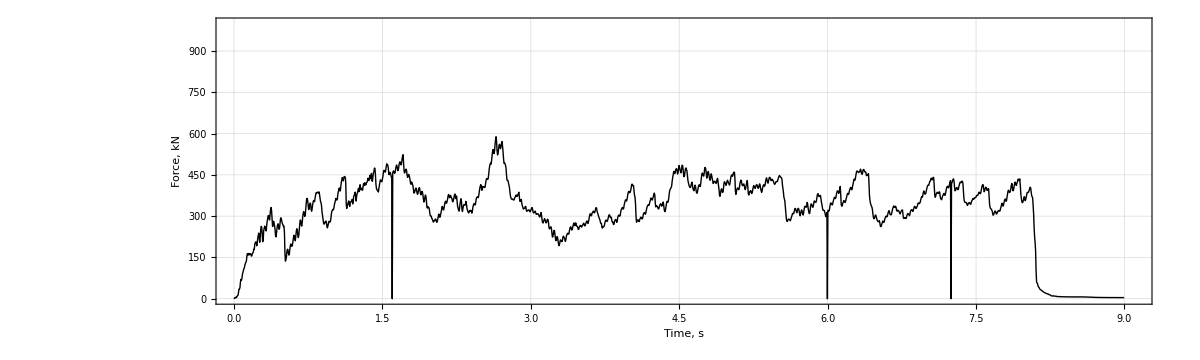

```mathematica
forceplot=ListLinePlot[Transpose[{tval,fval}],PlotTheme->"Detailed",AspectRatio->0.3,ImageSize->1200,FrameLabel->{{"Force, kN",""},{"Time, s",""}},PlotStyle->{{Thick,Black}},BaseStyle->{FontSize->25,FontFamily->"Times New Roman"},FrameStyle->Directive[Black],PlotRange->{{0,tval[[-1]]+0.1},{0,1000}},PlotLegends->None]
```

```mathematica
Export["force_plot.png",forceplot]
```

force_plot.png

```mathematica
index=1000;
```

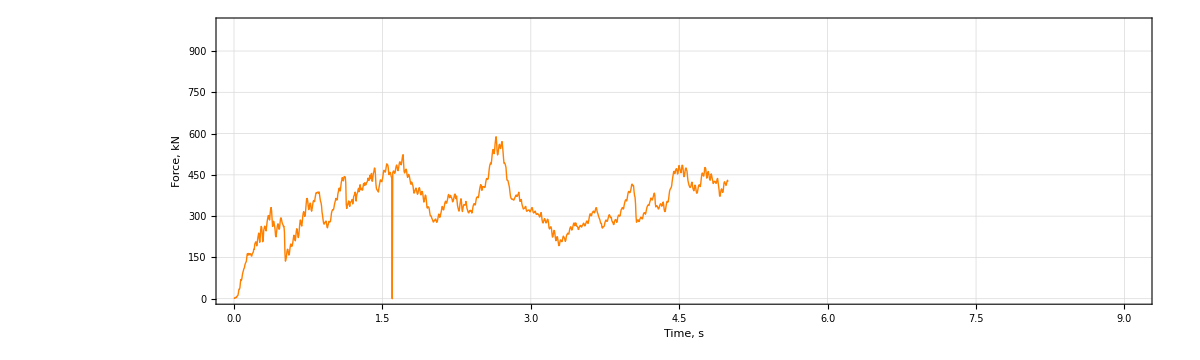

```mathematica
forceplot2=ListLinePlot[Transpose[{tval[[1;;index]],fval[[1;;index]]}],PlotTheme->"Detailed",AspectRatio->0.3,ImageSize->1200,FrameLabel->{{"Force, kN",""},{"Time, s",""}},PlotStyle->{{Thick,Orange}},BaseStyle->{FontSize->25,FontFamily->"Times New Roman"},FrameStyle->Directive[Black],PlotRange->{{0,tval[[-1]]+0.1},{0,1000}},PlotLegends->None]
```

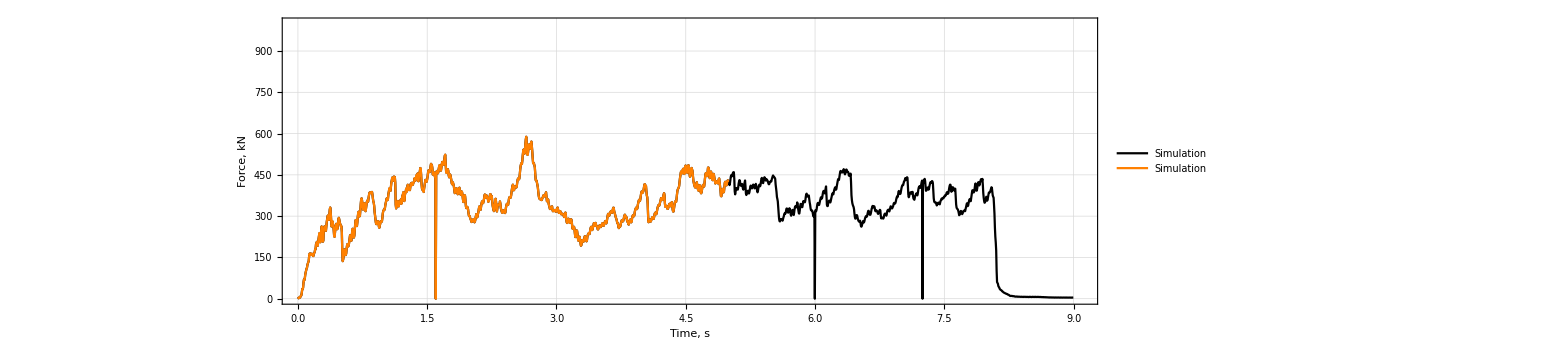

```mathematica
resultplot=Show[forceplot,forceplot2]
```

```mathematica
For[index=1,index<Length[tval],index++,forceplot2=ListLinePlot[Transpose[{tval[[1;;index]],fval[[1;;index]]}],PlotTheme->"Detailed",AspectRatio->0.3,ImageSize->1200,FrameLabel->{{"Force, kN",""},{"Time, s",""}},PlotStyle->{{Thick,Orange}},BaseStyle->{FontSize->25,FontFamily->"Times New Roman"},FrameStyle->Directive[Black],PlotRange->{{0,tval[[-1]]+0.1},{0,1000}},PlotLegends->None];resultplot=Show[forceplot,forceplot2];Export["force_"<>ToString[index]<>".png",resultplot];]
```